## Dipole v2, full |J|^2, GlobalAdaptive

```mathematica
Quit[];
```

### J2Fun

```mathematica
ClearAll[dir];
dir=FileNameJoin[{NotebookDirectory[],"Int"}]
```

/home/bwu/Documents/Dipole_v2_20230201/Int

```mathematica
Protect[ρ,η,k,b,x1,x2,x3,x4,I1a,I2a,I3a,I0a,SP];
```

```mathematica
ClearAll[I1NHuge,I1NLarge,I1NSmall,I2NHuge,I2NLarge,I2NSmall];
I1NHuge=<<(FileNameJoin[{dir,"I1NHuge"}]);
I1NLarge=<<(FileNameJoin[{dir,"I1NLarge"}]);
I1NSmall=<<(FileNameJoin[{dir,"I1NSmall"}]);
I2NHuge=<<(FileNameJoin[{dir,"I2NHuge"}]);
I2NLarge=<<(FileNameJoin[{dir,"I2NLarge"}]);
I2NSmall=<<(FileNameJoin[{dir,"I2NSmall"}]);
```

```mathematica
ClearAll[I1NLargeFun,I1NSmallFun,I2NLargeFun,I2NSmallFun];
I1NHugeFun=Interpolation[I1NHuge,InterpolationOrder->3,Method->"Hermite"];
I1NLargeFun=Interpolation[I1NLarge,InterpolationOrder->3,Method->"Hermite"];
I1NSmallFun=Interpolation[I1NSmall,InterpolationOrder->3,Method->"Hermite"];
I2NHugeFun=Interpolation[I2NHuge,InterpolationOrder->3,Method->"Hermite"];
I2NLargeFun=Interpolation[I2NLarge,InterpolationOrder->3,Method->"Hermite"];
I2NSmallFun=Interpolation[I2NSmall,InterpolationOrder->3,Method->"Hermite"];
```

Note the argument in I1NSmall and I2NSmall is ρ and Log[10,η]

```mathematica
ClearAll[I0Fun,I1Fun,I2Fun,I3Fun];
I0Fun=Compile[{{ρ,_Real},{η,_Real}},Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4Abs[ρ])]+EulerGamma),CompilationTarget->"WVM"];
I1Fun[ρ_,η_]:=Which[η<1/10,I1NSmallFun[ρ,Log[10,η]],η≥ 1/10&&η≤50,I1NLargeFun[ρ,η],True,I1NHugeFun[ρ,η]];
I2Fun[ρ_,η_]:=Which[η<1/10,I2NSmallFun[ρ,Log[10,η]],η≥1/10&&η≤50,I2NLargeFun[ρ,η],True,I2NHugeFun[ρ,η]];
I3Fun=Compile[{{ρ,_Real},{η,_Real}},-ⅈ/(4π)(1-Exp[ⅈ ρ η])Log[η]/(ρ η)];
```

```mathematica
ClearAll[J2Compile];
J2Compile=Compile[{{kx,_Real},{ky,_Real},{bx,_Real},{by,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{NSP,CoefList,I01b13,I01b23,I01b14,I01b24,I23b13,I23b23,I23b14,I23b24,IntList},
NSP[1]=bx^2+by^2;
NSP[2]=bx*x1x+by*x1y;
NSP[3]=bx*x2x+by*x2y;
NSP[4]=bx*x3x+by*x3y;
NSP[5]=bx*x4x+by*x4y;
NSP[6]=bx*kx+by*ky;
NSP[7]=kx^2+ky^2;
NSP[8]=kx*x1x+ky*x1y;
NSP[9]=kx*x2x+ky*x2y;
NSP[10]=kx*x3x+ky*x3y;
NSP[11]=kx*x4x+ky*x4y;
NSP[12]=x1x^2+x1y^2;
NSP[13]=x1x*x2x+x1y*x2y;
NSP[14]=x1x*x3x+x1y*x3y;
NSP[15]=x1x*x4x+x1y*x4y;
NSP[16]=x2x^2+x2y^2;
NSP[17]=x2x*x3x+x2y*x3y;
NSP[18]=x2x*x4x+x2y*x4y;
NSP[19]=x3x^2+x3y^2;
NSP[20]=x3x*x4x+x3y*x4y;
NSP[21]=x4x^2+x4y^2;

(*Print[Table[NSP[ii],{ii,1,21}]];*)

CoefList={{1,-E^((-I)*(NSP[8]-NSP[9])),-1,E^((-I)*(NSP[8]-NSP[9])),-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9])))},{-E^(I*(NSP[8]-NSP[9])),1,E^(I*(NSP[8]-NSP[9])),-1,E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11])),NSP[6]+NSP[9]-NSP[11]},{-1,E^((-I)*(NSP[8]-NSP[9])),1,-E^((-I)*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9])),-1,-E^(I*(NSP[8]-NSP[9])),1,-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10])),NSP[6]+NSP[9]-NSP[10],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11]),-NSP[6]-NSP[9]+NSP[11]},{-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[4]+NSP[12]-2*NSP[14]+NSP[19]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19]))/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]))/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10])),NSP[6]+NSP[9]-NSP[10],-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[4]+NSP[16]-2*NSP[17]+NSP[19]),E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20])},{NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9])),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]))/E^(I*(NSP[8]-NSP[9])),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[5]+NSP[12]-2*NSP[15]+NSP[21]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21]))/E^(I*(NSP[8]-NSP[9])))},{-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11])),NSP[6]+NSP[9]-NSP[11],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11]),-NSP[6]-NSP[9]+NSP[11],E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20]),-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[5]+NSP[16]-2*NSP[18]+NSP[21])}};

Module[{eta,rho},
eta=(((bx+x1x-x3x)(bx+x1x-x3x)+(by+x1y-x3y)(by+x1y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x3x)+ky(by+x1y-x3y))/eta;
I01b13=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b13=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x3x)(bx+x2x-x3x)+(by+x2y-x3y)(by+x2y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x3x)+ky(by+x2y-x3y))/eta;
I01b23=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b23=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x1x-x4x)(bx+x1x-x4x)+(by+x1y-x4y)(by+x1y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x4x)+ky(by+x1y-x4y))/eta;
I01b14=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b14=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x4x)(bx+x2x-x4x)+(by+x2y-x4y)(by+x2y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x4x)+ky(by+x2y-x4y))/eta;
I01b24=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b24=I2Fun[rho,eta]+I3Fun[rho,eta];
];


IntList={I01b13,I01b23,I01b14,I01b24,-ⅈ*I23b13,-ⅈ*I23b23,-ⅈ*I23b14,-ⅈ*I23b24};

(IntList.CoefList.ConjugateTranspose[{IntList}])[[1]]//Re
],
{{res,_Real}},CompilationTarget->"WVM",Parallelization->True
];



ClearAll[J2CompileN];
J2CompileN[kx_?NumericQ,ky_?NumericQ,bx_?NumericQ,by_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=J2Compile[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

### Code: DipoleV2bN

```mathematica
ClearAll[DipoleV2b];
DipoleV2b=Compile[{{k0,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{avg,avg2θk,precisiongoal,accuracygoal},

precisiongoal=6;
accuracygoal=6;

avg=NIntegrate[J2CompileN[k0 Cos[θk],k0 Sin[θk],0,0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y],{θk,0,2π},Method->"GlobalAdaptive"(*,WorkingPrecision->30*)(*,PrecisionGoal->precisiongoal, AccuracyGoal->accuracygoal*)];

avg2θk=NIntegrate[J2CompileN[k0 Cos[θk],k0 Sin[θk],0,0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]Cos[2θk],{θk,0,2π},Method->"GlobalAdaptive"(*,WorkingPrecision->30*)(*,PrecisionGoal->precisiongoal, AccuracyGoal->accuracygoal*)];

avg2θk/avg

],
{{res,_Real}},CompilationTarget->"WVM",Parallelization->True
];


ClearAll[DipoleV2bN];
DipoleV2bN[k0_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=DipoleV2b[k0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

### Code: DipoleSigmaN

```mathematica
ClearAll[DipoleSigma];
DipoleSigma=Compile[{{k0,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{avg,avg2θk,precisiongoal,accuracygoal},

precisiongoal=6;
accuracygoal=6;

avg=NIntegrate[J2CompileN[k0 Cos[θk],k0 Sin[θk],0,0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y],{θk,0,2π},Method->"GlobalAdaptive"(*,WorkingPrecision->30*)(*,PrecisionGoal->precisiongoal, AccuracyGoal->accuracygoal*)];

(*avg2θk=NIntegrate[J2CompileN[k0 Cos[θk],k0 Sin[θk],0,0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]Cos[2θk],{θk,0,2π},Method->"GlobalAdaptive"(*,WorkingPrecision->30*)(*,PrecisionGoal->precisiongoal, AccuracyGoal->accuracygoal*)];*)

avg

],
{{res,_Real}},CompilationTarget->"WVM",Parallelization->True
];


ClearAll[DipoleSigmaN];
DipoleSigmaN[k0_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=DipoleSigma[k0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

### test 1

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
by=1;
rA=0.1;
rAθ=0;
rB=0.1;
rBθ=0(*π/4*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
```

```mathematica
ClearAll[ti,temp1];
ti=AbsoluteTime[];
temp1=Table[{k,DipoleV2bN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

99.6441924

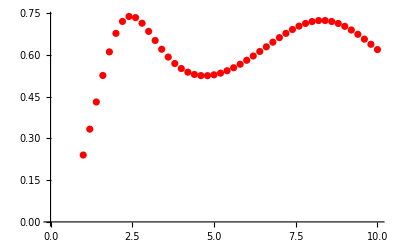

```mathematica
ListPlot[temp1,PlotStyle->Red]
```

```mathematica
ClearAll[ti,temp2];
ti=AbsoluteTime[];
temp2=Table[{k,DipoleSigmaN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

49.0466562

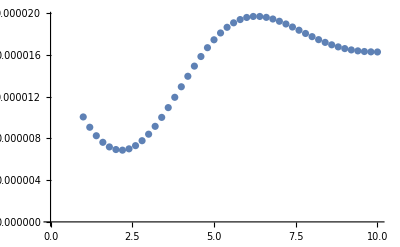

```mathematica
ListPlot[temp2]
```

### test 2

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
by=1;
rA=1;
rAθ=0;
rB=1;
rBθ=0(*π/4*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
```

```mathematica
ClearAll[ti,temp1];
ti=AbsoluteTime[];
temp1=Table[{k,DipoleV2bN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

77.9518399

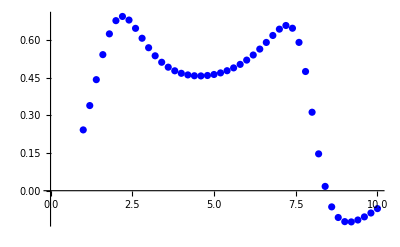

```mathematica
ListPlot[temp1,PlotStyle->Blue]
```

```mathematica
ClearAll[ti,temp2];
ti=AbsoluteTime[];
temp2=Table[{k,DipoleSigmaN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

28.342785

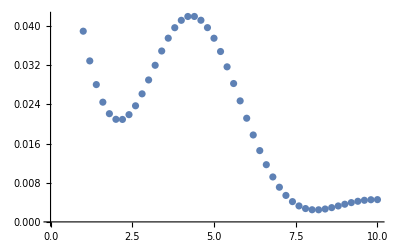

```mathematica
ListPlot[temp2]
```

### test 3

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
by=1;
rA=2;
rAθ=0;
rB=2;
rBθ=0(*π/4*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
```

```mathematica
ClearAll[ti,temp1];
ti=AbsoluteTime[];
temp1=Table[{k,DipoleV2bN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

98.2155183

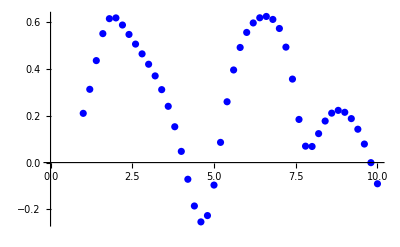

```mathematica
ListPlot[temp1,PlotStyle->Blue]
```

```mathematica
ClearAll[ti,temp2];
ti=AbsoluteTime[];
temp2=Table[{k,DipoleSigmaN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

28.269159

```mathematica
ListPlot[temp2]
```

-Graphics-

## Dipole v_2

### Scalings: v_2 for (b=10, r_dp=1) and for (b=1, r_dp=0.1)

```mathematica
Getv2kT[b_]:=Module[{bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y,ti,b02},
bx=b;
by=0;
rA=1.0;
rAθ=π/2;
rB=1.0;
rBθ=π/2(*π/4*);
x1x=bx/2+rA/2 Cos[rAθ];
x1y=by/2+rA/2 Sin[rAθ];
x2x=bx/2-rA/2 Cos[rAθ];
x2y=by/2-rA/2 Sin[rAθ];
x3x=-bx/2+rB/2 Cos[rBθ];
x3y=-by/2+rB/2 Sin[rBθ];
x4x=-bx/2-rB/2 Cos[rBθ];
x4y=-by/2-rB/2 Sin[rBθ];
ClearAll[ti,b02];
ti=AbsoluteTime[];
b02=ParallelTable[{k,DipoleV2bN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,0.025,3.0,0.025}]//Quiet;
Print["For b = ",b," Computation time: ",AbsoluteTime[]-ti];
Print[ListPlot[b02,PlotStyle->Red]];
b02
]
```

```mathematica
LaunchKernels[24]
$KernelCount
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

24

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.13551}. NIntegrate obtained 0.0000170753 and 1.88499×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.17862}. NIntegrate obtained 0.0000136799 and 3.64085×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.14118}. NIntegrate obtained 0.0000135038 and 6.05603×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {2.17202}. NIntegrate obtained 0.0000142454 and 1.91514×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {2.09839}. NIntegrate obtained 0.0000137288 and 3.40629×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.38724}. NIntegrate obtained 0.0000138714 and 2.34006×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {2.00021}. NIntegrate obtained 0.0000132886 and 2.94037×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {0.809844}. NIntegrate obtained 0.0000160452 and 1.91772×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.38724}. NIntegrate obtained 0.0000137156 and 2.9427×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.20254}. NIntegrate obtained 0.0000123883 and 5.40796×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.42406}. NIntegrate obtained 0.000016333 and 2.65532×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.42406}. NIntegrate obtained 0.0000130103 and 3.64658×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.17862}. NIntegrate obtained -6.43531×10^-6 and 1.87548×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.24596}. NIntegrate obtained 0.0000118909 and 4.63949×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.178}. NIntegrate obtained 0.0000126985 and 4.41487×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {2.00021}. NIntegrate obtained -6.17493×10^-6 and 1.68595×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {2.08612}. NIntegrate obtained 0.0000121117 and 3.76869×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {2.01249}. NIntegrate obtained -6.22383×10^-6 and 3.51723×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.98227}. NIntegrate obtained 0.0000136405 and 2.89088×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.4848}. NIntegrate obtained -7.31644×10^-6 and 1.85977×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.00682}. NIntegrate obtained -8.13524×10^-6 and 1.01811×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.20254}. NIntegrate obtained -6.16714×10^-6 and 3.13022×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.24596}. NIntegrate obtained -5.98437×10^-6 and 2.56385×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {0.920291}. NIntegrate obtained 0.0000150581 and 2.10731×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.79159}. NIntegrate obtained -7.77844×10^-6 and 8.37045×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.08045}. NIntegrate obtained 0.0000116264 and 7.68866×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {2.0493}. NIntegrate obtained 0.0000117319 and 5.77522×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.76705}. NIntegrate obtained -9.04835×10^-6 and 1.81087×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.12953}. NIntegrate obtained -6.17172×10^-6 and 1.96687×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.79159}. NIntegrate obtained 0.0000140933 and 2.92627×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.20915}. NIntegrate obtained 0.0000137169 and 3.34725×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.41116}. NIntegrate obtained 0.0000131557 and 4.08106×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.15346}. NIntegrate obtained 0.0000134051 and 3.39404×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.38724}. NIntegrate obtained -6.8236×10^-6 and 8.00332×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.46087}. NIntegrate obtained 0.0000158888 and 2.09252×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.88977}. NIntegrate obtained -6.18036×10^-6 and 2.97217×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.77365}. NIntegrate obtained -6.10593×10^-6 and 2.08715×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.58359}. NIntegrate obtained 0.0000122448 and 7.47966×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.24596}. NIntegrate obtained 0.0000115534 and 4.68348×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.79159}. NIntegrate obtained -8.00322×10^-6 and 2.11146×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.22771}. NIntegrate obtained 0.0000118037 and 3.63451×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.08045}. NIntegrate obtained -5.58334×10^-6 and 4.6997×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.20915}. NIntegrate obtained 0.000011486 and 9.44634×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {2.08612}. NIntegrate obtained 0.0000113926 and 9.38392×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.03074}. NIntegrate obtained 0.0000138014 and 2.42648×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.9634}. NIntegrate obtained 0.0000125412 and 8.6911×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {2.25792}. NIntegrate obtained 0.0000137132 and 3.25206×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {2.0493}. NIntegrate obtained -5.80471×10^-6 and 3.34988×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.12324}. NIntegrate obtained 0.0000128562 and 6.85186×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.22142}. NIntegrate obtained 0.0000112586 and 4.52043×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.20915}. NIntegrate obtained 0.0000119935 and 3.292×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.81614}. NIntegrate obtained 0.000011073 and 4.79136×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.97567}. NIntegrate obtained 0.0000108405 and 6.35022×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.80386}. NIntegrate obtained 0.000010576 and 1.11368×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.41116}. NIntegrate obtained -5.34565×10^-6 and 3.29337×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {2.08612}. NIntegrate obtained -4.92547×10^-6 and 5.11387×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {2.02476}. NIntegrate obtained -5.11968×10^-6 and 6.12172×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.11664}. NIntegrate obtained 0.00001004 and 1.12595×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.33753}. NIntegrate obtained 9.62179×10^-6 and 1.64534×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.25823}. NIntegrate obtained 9.80995×10^-6 and 7.56259×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {2.02476}. NIntegrate obtained 0.0000103013 and 7.09793×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.33753}. NIntegrate obtained -4.78157×10^-6 and 2.77034×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {2.0493}. NIntegrate obtained 0.0000116737 and 5.38294×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.20915}. NIntegrate obtained 0.0000115875 and 5.16375×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.93318}. NIntegrate obtained 9.35885×10^-6 and 2.33031×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.80386}. NIntegrate obtained -4.60363×10^-6 and 7.70522×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.28278}. NIntegrate obtained 9.47518×10^-6 and 8.64175×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.81614}. NIntegrate obtained -4.68793×10^-6 and 3.61968×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.88977}. NIntegrate obtained 0.000011519 and 1.00347×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.97567}. NIntegrate obtained -4.63485×10^-6 and 3.87719×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.33753}. NIntegrate obtained -4.2925×10^-6 and 1.33384×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.86522}. NIntegrate obtained 0.0000111723 and 1.19471×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.11664}. NIntegrate obtained -4.51645×10^-6 and 5.88736×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.93318}. NIntegrate obtained -3.93262×10^-6 and 1.66543×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.25823}. NIntegrate obtained -4.4254×10^-6 and 3.48939×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.27617}. NIntegrate obtained 0.0000113319 and 7.37869×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {0.674854}. NIntegrate obtained 9.25548×10^-6 and 8.72262×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.86522}. NIntegrate obtained 0.0000109619 and 8.43891×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {2.02476}. NIntegrate obtained -4.5712×10^-6 and 3.38121×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.76138}. NIntegrate obtained 0.000010438 and 1.58042×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.06755}. NIntegrate obtained 0.0000114429 and 4.75756×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.28278}. NIntegrate obtained -4.12376×10^-6 and 8.06078×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.47913}. NIntegrate obtained 9.54384×10^-6 and 1.36189×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.99454}. NIntegrate obtained 0.000010711 and 8.41042×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.46685}. NIntegrate obtained 9.91967×10^-6 and 7.21969×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {3.81645}. NIntegrate obtained 9.14606×10^-6 and 8.38764×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.17862}. NIntegrate obtained 9.7105×10^-6 and 9.11555×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {3.76736}. NIntegrate obtained 9.41394×10^-6 and 5.7881×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.55276}. NIntegrate obtained -3.73727×10^-6 and 5.2648×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {0.674854}. NIntegrate obtained 9.30659×10^-6 and 1.12301×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.17862}. NIntegrate obtained 0.0000101673 and 7.2142×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {4.8841}. NIntegrate obtained -3.55717×10^-6 and 5.28315×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {1.16573}. NIntegrate obtained 9.08397×10^-6 and 1.6104×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θk near {θk} = {5.62041}. NIntegrate obtained 9.20277×10^-6 and 8.71456×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For b = 10 Computation time: 1386.39852

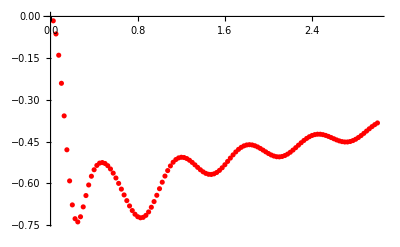

{{0.025,-0.0157187},{0.05,-0.062827},{0.075,-0.139328},{0.1,-0.240227},{0.125,-0.35739},{0.15,-0.479261},{0.175,-0.591091},{0.2,-0.677349},{0.225,-0.726966},{0.25,-0.738423},{0.275,-0.719943},{0.3,-0.684442},{0.325,-0.643735},{0.35,-0.605698},{0.375,-0.574323},{0.4,-0.550945},{0.425,-0.535463},{0.45,-0.527157},{0.475,-0.525121},{0.5,-0.528467},{0.525,-0.536388},{0.55,-0.548162},{0.575,-0.563122},{0.6,-0.580625},{0.625,-0.600009},{0.65,-0.620565},{0.675,-0.641511},{0.7,-0.661978},{0.725,-0.681019},{0.75,-0.697642},{0.775,-0.710858},{0.8,-0.719767},{0.825,-0.723653},{0.85,-0.722076},{0.875,-0.714966},{0.9,-0.702631},{0.925,-0.685778},{0.95,-0.665429},{0.975,-0.642763},{1.,-0.619111},{1.025,-0.595719},{1.05,-0.573702},{1.075,-0.553992},{1.1,-0.53727},{1.125,-0.523987},{1.15,-0.514373},{1.175,-0.50846},{1.2,-0.506108},{1.225,-0.507021},{1.25,-0.510778},{1.275,-0.516844},{1.3,-0.524609},{1.325,-0.533384},{1.35,-0.542427},{1.375,-0.551004},{1.4,-0.558401},{1.425,-0.56399},{1.45,-0.567259},{1.475,-0.567875},{1.5,-0.565682},{1.525,-0.560756},{1.55,-0.553334},{1.575,-0.543873},{1.6,-0.532927},{1.625,-0.521115},{1.65,-0.509113},{1.675,-0.497507},{1.7,-0.486919},{1.725,-0.47777},{1.75,-0.470421},{1.775,-0.46511},{1.8,-0.461929},{1.825,-0.460896},{1.85,-0.461883},{1.875,-0.464681},{1.9,-0.46897},{1.925,-0.474371},{1.95,-0.48043},{1.975,-0.4867},{2.,-0.492639},{2.025,-0.49782},{2.05,-0.501737},{2.075,-0.504133},{2.1,-0.50468},{2.125,-0.503273},{2.15,-0.499926},{2.175,-0.49478},{2.2,-0.488089},{2.225,-0.480229},{2.25,-0.471636},{2.275,-0.46269},{2.3,-0.453883},{2.325,-0.445733},{2.35,-0.438406},{2.375,-0.432338},{2.4,-0.427743},{2.425,-0.424703},{2.45,-0.423252},{2.475,-0.423365},{2.5,-0.42485},{2.525,-0.427551},{2.55,-0.431117},{2.575,-0.435291},{2.6,-0.439572},{2.625,-0.44375},{2.65,-0.447275},{2.675,-0.449846},{2.7,-0.45121},{2.725,-0.451113},{2.75,-0.449424},{2.775,-0.446123},{2.8,-0.441333},{2.825,-0.435217},{2.85,-0.42805},{2.875,-0.420203},{2.9,-0.411968},{2.925,-0.40379},{2.95,-0.396003},{2.975,-0.388929},{3.,-0.38282}}

```mathematica
Getv2kT[10]
```

```mathematica
v2b10:={{0.025,-0.015718719721178314},{0.05,-0.06282700520492344},{0.07500000000000001,-0.13932777556630255},{0.1,-0.24022686596223616},{0.125,-0.3573898070753249},{0.15000000000000002,-0.47926133318519265},{0.17500000000000002,-0.5910905844385032},{0.2,-0.6773485071214307},{0.22500000000000003,-0.7269659742709673},{0.25,-0.7384228508931457},{0.275,-0.7199432377383406},{0.3,-0.6844423879227562},{0.32500000000000007,-0.6437348216132235},{0.3500000000000001,-0.6056977704529468},{0.37500000000000006,-0.5743230810972393},{0.4,-0.5509450813008779},{0.42500000000000004,-0.5354634711787141},{0.45,-0.5271569742815208},{0.47500000000000003,-0.5251213439486991},{0.5,-0.5284673400168799},{0.525,-0.5363884128227737},{0.55,-0.5481620285704647},{0.5750000000000001,-0.5631222515579},{0.6000000000000001,-0.5806247305758189},{0.6250000000000001,-0.6000091086422754},{0.6500000000000001,-0.6205652794318244},{0.6750000000000002,-0.6415112440414693},{0.7000000000000001,-0.6619780296718993},{0.7250000000000001,-0.6810190635679686},{0.7500000000000001,-0.697642450560904},{0.775,-0.7108584400082162},{0.8,-0.7197674742524524},{0.8250000000000001,-0.7236530530051561},{0.8500000000000001,-0.7220755757409717},{0.8750000000000001,-0.7149657237731349},{0.9000000000000001,-0.7026313798074617},{0.925,-0.6857778377710074},{0.9500000000000001,-0.6654285735793853},{0.9750000000000001,-0.6427632459378968},{1.,-0.6191110639480277},{1.025,-0.5957188246440537},{1.05,-0.5737015050372748},{1.075,-0.5539916214788262},{1.0999999999999999,-0.5372698734812836},{1.125,-0.5239872611308002},{1.15,-0.5143725975495175},{1.1749999999999998,-0.5084597678728341},{1.2,-0.5061075684240184},{1.225,-0.5070213530126287},{1.25,-0.510777510724093},{1.2750000000000001,-0.5168437693876898},{1.3,-0.5246091726287541},{1.325,-0.5333844134675875},{1.35,-0.5424269721690551},{1.375,-0.5510037268678667},{1.4,-0.5584008919648592},{1.425,-0.5639898471471393},{1.45,-0.567258624265024},{1.4749999999999999,-0.5678747986966131},{1.5,-0.5656816070173833},{1.525,-0.5607555255183843},{1.5499999999999998,-0.5533341837568585},{1.575,-0.5438728526359531},{1.6,-0.532926866517002},{1.625,-0.5211152931915941},{1.6500000000000001,-0.5091125901884824},{1.675,-0.4975069435125121},{1.7,-0.48691881104526324},{1.725,-0.4777704584557226},{1.75,-0.47042114951077085},{1.775,-0.46510988562134215},{1.8,-0.46192867318184183},{1.825,-0.4608957887623679},{1.8499999999999999,-0.46188347308120997},{1.875,-0.46468060214696866},{1.9,-0.4689695643054051},{1.925,-0.4743706366449956},{1.95,-0.4804303341133662},{1.975,-0.48669984226306945},{2.,-0.4926391948866762},{2.025,-0.4978198385421345},{2.05,-0.501736954733991},{2.075,-0.504133425912999},{2.1,-0.5046801237408856},{2.125,-0.5032732619523134},{2.15,-0.4999257160910625},{2.175,-0.4947798164342305},{2.1999999999999997,-0.48808901500134966},{2.225,-0.48022931545706915},{2.25,-0.47163586683161485},{2.275,-0.4626898629693921},{2.3,-0.4538833138990914},{2.325,-0.44573267120519244},{2.35,-0.438405775747714},{2.375,-0.43233849360065013},{2.4,-0.4277432925311573},{2.4250000000000003,-0.4247031567019745},{2.45,-0.42325230217851334},{2.475,-0.4233649059889643},{2.5,-0.4248504725591249},{2.525,-0.4275508860452181},{2.55,-0.43111710009662835},{2.575,-0.43529145102835587},{2.6,-0.43957192800693634},{2.625,-0.4437503089254097},{2.65,-0.44727461468614965},{2.6750000000000003,-0.4498461640692474},{2.7,-0.45121017341819086},{2.725,-0.45111319996300736},{2.75,-0.4494241419611976},{2.775,-0.4461227329797742},{2.8,-0.44133301091586197},{2.825,-0.4352168639917947},{2.85,-0.4280499123942391},{2.875,-0.42020320696963126},{2.9,-0.41196812483009515},{2.9250000000000003,-0.4037898836850741},{2.95,-0.3960027985608253},{2.975,-0.3889291027409209},{3.,-0.382819848889614}}
```

```mathematica
v2kTr01:={{0.125,{-0.003918057710614559,9.244854885711647*^-15}},{0.25,{-0.015718719721257,4.455768613178577*^-15}},{0.375,{-0.035404393455990855,-3.24942552743455*^-14}},{0.5,{-0.06282700520498571,-9.209262174235287*^-12}},{0.625,{-0.09764251133096699,1.1323373487828947*^-11}},{0.75,{-0.13932777556625237,-2.0075541724325464*^-13}},{0.875,{-0.1871596950255955,3.6587891032648094*^-14}},{1.,{-0.2402268659614949,1.7761272106741705*^-12}},{1.125,{-0.29741608683685067,1.63936386445259*^-12}},{1.25,{-0.35738980707365536,-2.9331080873408746*^-14}},{1.375,{-0.41860210294753264,5.5624657311130876*^-14}},{1.5,{-0.4792613331839505,2.1483054629612167*^-11}},{1.625,{-0.5374405029017671,-4.33280410886713*^-12}},{1.75,{-0.5910905844362639,7.782502667849232*^-10}},{1.875,{-0.6382657283683378,-1.6304778766370707*^-13}},{2.,{-0.6773485071187965,-1.1020930550360381*^-13}},{2.125,{-0.7070922567638241,-2.2980585681298934*^-14}},{2.25,{-0.7269659742677628,2.704041641059906*^-14}},{2.375,{-0.7371361605396004,6.273889630496712*^-14}},{2.5,{-0.7384228508900981,1.0598538605139731*^-13}},{2.625,{-0.7321427588980837,6.659595237400903*^-14}},{2.75,{-0.7199432377360689,-4.260275997313958*^-14}},{2.875,{-0.7034905063569131,-5.247259673659533*^-15}},{3.,{-0.6844423879210192,-2.1853706117116236*^-10}},{3.125,{-0.6641124978889632,2.067040341464235*^-7}},{3.25,{-0.6437348216121175,-1.2554414576815327*^-6}},{3.375,{-0.6240287203305982,2.3379570679486058*^-9}},{3.5,{-0.6056977704518648,-1.7925891529668374*^-14}},{3.625,{-0.5890209403411332,3.1520035514624035*^-15}},{3.75,{-0.5743230810965477,-4.1466113956369136*^-14}},{3.875,{-0.5615908182140499,3.648522336489531*^-14}},{4.,{-0.5509450813004367,1.7927726800391485*^-14}},{4.125,{-0.5422263685405077,1.0903453666383883*^-14}},{4.25,{-0.535463471178256,1.70266968146611*^-14}},{4.375,{-0.5304417121950176,4.759113761210206*^-14}},{4.5,{-0.5271569742812412,3.128951738783436*^-14}},{4.625,{-0.5253862269155424,3.598453744249841*^-14}},{4.75,{-0.5251213439483727,-2.428438280829479*^-15}},{4.875,{-0.5261507000273551,2.740499076043137*^-14}},{5.,{-0.5284673400166482,2.3894269069901594*^-14}},{5.125,{-0.5318829019586997,1.149190308111416*^-15}},{5.25,{-0.5363884128225829,2.1134322259835257*^-8}},{5.375,{-0.5418199157681947,1.2010731556825687*^-14}},{5.5,{-0.5481620285702847,1.1148763365957442*^-14}},{5.625,{-0.5552737445041922,-8.207069955019638*^-15}},{5.75,{-0.5631222515577617,5.397564812856081*^-15}},{5.875,{-0.5715864634218168,7.414484970014047*^-15}},{6.,{-0.5806247305756812,4.77842247006239*^-15}},{6.125,{-0.5901175885917581,1.3616455397502957*^-14}},{6.25,{-0.6000091086421262,4.352458936126006*^-15}},{6.375,{-0.6101831594975383,6.646937432759431*^-15}},{6.5,{-0.6205652794316837,-3.958075861245624*^-15}},{6.625,{-0.6310351690619019,-0.000018677847951257842}},{6.75,{-0.641511244041416,4.962331055710025*^-15}},{6.875,{-0.6518606611667205,2.554591094168787*^-15}},{7.,{-0.6619780296717406,1.0836216739777441*^-14}},{7.125,{-0.6717382011865476,-2.9290169948253282*^-15}},{7.25,{-0.6810190635678771,1.3639273580277793*^-14}},{7.375,{-0.6896961869618619,6.943860915145641*^-15}},{7.5,{-0.6976424505607638,-1.318541182628416*^-14}},{7.625,{-0.7047345966199451,5.447913040411827*^-15}},{7.75,{-0.7108584400080679,-2.0925760370717457*^-14}},{7.875,{-0.7159012569390238,-9.91784094948124*^-15}},{8.,{-0.7197674742523701,-1.2440075599238084*^-15}},{8.125,{-0.7223729235444168,1.0561550325913656*^-14}},{8.25,{-0.7236530530050557,-1.3847475036530753*^-14}},{8.375,{-0.7235617043911938,-1.0385721845199884*^-6}},{8.5,{-0.7220755757408699,2.287960614425298*^-14}},{8.625,{-0.7192036223031588,-8.35843469193545*^-15}},{8.75,{-0.7149657237731009,2.027975084614235*^-6}},{8.875,{-0.7094169934332586,-5.231311626546625*^-15}},{9.,{-0.7026313798074314,1.2891481340484175*^-7}},{9.125,{-0.6947167039601682,-2.147836268823866*^-14}},{9.25,{-0.685777837770821,7.096383091306253*^-15}},{9.375,{-0.676018020597335,5.709536337482595*^-10}},{9.5,{-0.6654285735792814,-8.581145590162497*^-8}},{9.625,{-0.654289558294374,4.160395754737705*^-9}},{9.75,{-0.6427632459378138,1.7996043544820085*^-9}},{9.875,{-0.6309636673004227,4.226048165496085*^-10}},{10.,{-0.6191110639479821,7.595792922208492*^-9}},{10.125,{-0.6072917387608915,-2.638841929245373*^-9}},{10.25,{-0.5957188246440015,-3.1015597792991535*^-9}},{10.375,{-0.5844645343467849,-1.551269967745795*^-8}},{10.5,{-0.57370150503722,-4.4371818780436207*^-7}},{10.625,{-0.5635097362380815,1.8552656231098774*^-9}},{10.75,{-0.5539916214788152,4.0395969162598574*^-14}},{10.875,{-0.5452226924354484,-1.780511057889443*^-14}},{11.,{-0.5372698734812158,-4.744145593705214*^-9}},{11.125,{-0.5301790327086909,4.195848666449436*^-14}},{11.25,{-0.5239872611307822,2.728685607364563*^-14}},{11.375,{-0.5187128507420379,2.4422684108623936*^-14}},{11.5,{-0.5143725975494813,-3.496286680063301*^-14}},{11.625,{-0.510955748904712,-2.0664917798758742*^-14}},{11.75,{-0.5084597678727364,2.7881696845516474*^-14}},{11.875,{-0.5068530909992728,3.1142175367135745*^-14}},{12.,{-0.5061075684239557,-1.461442305709657*^-14}},{12.125,{-0.5061716891195183,4.0825170656166505*^-14}},{12.25,{-0.5070213530125814,2.1860598265125716*^-14}},{12.375,{-0.5085695649902339,5.423487024647039*^-14}},{12.5,{-0.510777510724057,-3.7298607318384654*^-14}},{12.625,{-0.5135580520205365,-2.7144829964143545*^-14}},{12.75,{-0.516843769387631,3.905077961491842*^-14}},{12.875,{-0.5205564772213358,-5.953200852970119*^-6}},{13.,{-0.5246091726286898,2.113148931274359*^-14}},{13.125,{-0.5289076310929574,-1.2054313735626946*^-14}},{13.25,{-0.5333844134675617,2.883326672743894*^-15}},{13.375,{-0.5379172659817382,3.56506201745071*^-14}},{13.5,{-0.5424269721690292,-5.1064580363419865*^-14}},{13.625,{-0.546815862479167,-3.2318346559616534*^-14}},{13.75,{-0.551003726867789,2.1615203883493048*^-6}},{13.875,{-0.5548861803313295,6.620780524955221*^-14}},{14.,{-0.5584008919648269,-5.688665305842023*^-9}},{14.125,{-0.5614709362637526,-2.897494281422422*^-9}},{14.25,{-0.5639898471470772,-4.1928217124719556*^-14}},{14.375,{-0.5659324345221263,-3.4531692542762257*^-14}},{14.5,{-0.5672586242649905,-4.807176917575697*^-14}},{14.625,{-0.5679067183134074,2.4104502828648115*^-14}},{14.75,{-0.5678747986966025,4.710647930983182*^-14}},{14.875,{-0.5671169769243197,3.72258226325579*^-14}},{15.,{-0.5656816070173624,8.06852755841809*^-15}},{15.125,{-0.5635384254091744,-7.510508136295701*^-14}},{15.25,{-0.56075552551836,1.25152175074836*^-14}},{15.375,{-0.5573004513694695,3.5590212147582575*^-14}},{15.5,{-0.5533341837568391,9.577606751690335*^-10}},{15.625,{-0.5488184443536331,-4.8080410027081485*^-14}},{15.75,{-0.5438728526359264,-9.584287837352239*^-15}},{15.875,{-0.5385484248118637,9.3955412023375*^-8}},{16.,{-0.5329268665170057,-3.8792326671220296*^-15}},{16.125,{-0.527067341734732,4.655757932398242*^-14}},{16.25,{-0.5211152931915697,-6.7995068199288484*^-15}},{16.375,{-0.5150812721601088,5.548916646547927*^-9}},{16.5,{-0.5091125901884977,8.011336983399773*^-14}},{16.625,{-0.503210597506499,2.7218779042229064*^-7}},{16.75,{-0.49750694351250224,-3.772022823975667*^-14}},{16.875,{-0.4920537949899836,-1.2511884263301538*^-14}},{17.,{-0.48691881104524515,-5.345949023786466*^-14}},{17.125,{-0.4821307158749294,-7.410663561568436*^-15}},{17.25,{-0.47777045845568183,3.7434932908790614*^-15}},{17.375,{-0.47384415636903865,5.966703863615523*^-15}},{17.5,{-0.4704211495107554,7.532302330341834*^-14}},{17.625,{-0.46749090679274174,4.390700693813543*^-14}},{17.75,{-0.4651098856213215,-4.735876892443972*^-15}},{17.875,{-0.46324289313407163,-2.104956549555236*^-8}},{18.,{-0.4619286731818374,-4.030065275947804*^-14}},{18.125,{-0.461149077605719,-6.542881813006678*^-14}},{18.25,{-0.460895788762363,2.940479971703702*^-6}},{18.375,{-0.46113375363503656,-1.980772529508429*^-14}},{18.5,{-0.461883473081167,-2.0897297555967427*^-14}},{18.625,{-0.46307099222403986,6.681066146310082*^-14}},{18.75,{-0.46468060214693285,-1.177628293229202*^-14}},{18.875,{-0.4666571776539901,-1.7086602708282606*^-8}},{19.,{-0.46896956430538544,-3.828063149989548*^-14}},{19.125,{-0.4715519322773859,1.2322568083549429*^-14}},{19.25,{-0.4743706366449681,1.8680041343858585*^-14}},{19.375,{-0.4773503356144509,9.278299313068467*^-14}},{19.5,{-0.480430334113364,1.0318391124324963*^-13}},{19.625,{-0.4835823912600917,-5.14004639915888*^-14}},{19.75,{-0.4866998422630719,-1.7287423727555124*^-14}},{19.875,{-0.4897457666307268,-1.597230991496991*^-14}},{20.,{-0.4926391948866737,-3.25636684229374*^-6}},{20.125,{-0.4953630392999924,7.63791365314107*^-15}},{20.25,{-0.4978198385421389,-7.17621977032122*^-14}},{20.375,{-0.4999851266323586,-1.5741426666256957*^-14}},{20.5,{-0.5017369547339656,9.254957801709921*^-15}},{20.625,{-0.5031636579503245,-4.2779378693736176*^-14}},{20.75,{-0.5041334259129382,-4.9393755943928894*^-8}},{20.875,{-0.5046489107715457,4.76288951391161*^-8}},{21.,{-0.5046801237408688,5.344459368659944*^-8}},{21.125,{-0.504223877709701,-5.5449739133984515*^-8}},{21.25,{-0.5032732619523007,6.489640882211827*^-14}},{21.375,{-0.5018302417174715,-6.033401053662525*^-14}},{21.5,{-0.49992571609102104,6.127152660289473*^-8}},{21.625,{-0.49755516133334904,6.920669434659163*^-14}},{21.75,{-0.4947798164341914,8.203047498184611*^-15}},{21.875,{-0.49159876889154186,3.7752479276997184*^-14}},{22.,{-0.4880890150013355,2.6180097567770878*^-8}},{22.125,{-0.4842748163077433,-5.5482811489787554*^-14}},{22.25,{-0.4802293154570574,-5.377307437107822*^-14}},{22.375,{-0.4759754602071142,3.364912282960911*^-14}},{22.5,{-0.471635866831603,-2.3764486157273692*^-8}},{22.625,{-0.4671447714425382,-1.3016389315369388*^-13}},{22.75,{-0.46268986296936804,-7.619666953358566*^-8}},{22.875,{-0.45823245579980426,-8.475776061132287*^-8}},{23.,{-0.45388331389909664,-4.358226719250919*^-14}},{23.125,{-0.4496261773431517,1.2981206420934466*^-13}},{23.25,{-0.4457326712051796,9.618772204798758*^-8}},{23.375,{-0.44191434974351523,-1.3708939314195487*^-6}},{23.5,{-0.4384057757477033,-6.452133754270889*^-8}},{23.625,{-0.4352000848031097,4.343737142225139*^-15}},{23.75,{-0.4323384936006302,-2.374703016560287*^-13}},{23.875,{-0.4298464001530676,-2.6835303414091216*^-6}},{24.,{-0.42774329253115484,-9.237924090252065*^-8}},{24.125,{-0.4260122730013701,-1.6037490877630148*^-13}},{24.25,{-0.4247031567019669,4.409930619066391*^-14}},{24.375,{-0.42376795667412026,6.273343426917469*^-14}},{24.5,{-0.4232523021784899,-1.1754861454399368*^-14}},{24.625,{-0.42311307956741384,3.0058374124292336*^-7}},{24.75,{-0.4233649059889497,3.092283985634873*^-7}},{24.875,{-0.42392298901895437,-2.368480464842721*^-14}},{25.,{-0.42485047255910835,-3.946606557341267*^-14}},{25.125,{-0.42606027925299195,-3.282572556989622*^-7}},{25.25,{-0.42755088604521085,5.4730319659071236*^-17}},{25.375,{-0.4292463383192781,-1.1874230210186027*^-14}},{25.5,{-0.4311171000966129,-7.256387564780687*^-15}},{25.625,{-0.43314686190293206,-1.2070281234177507*^-7}},{25.75,{-0.43529145102834615,-2.881805837704058*^-14}},{25.875,{-0.4374557756665144,-2.9449024212099173*^-8}},{26.,{-0.43957192800694617,-1.2197409264483674*^-14}},{26.125,{-0.441722961502819,4.654125022016889*^-8}},{26.25,{-0.443750308925389,-1.4635979953332415*^-8}},{26.375,{-0.44560321163111033,7.768982996323666*^-7}},{26.5,{-0.44727461468616014,-1.2411452655714186*^-6}},{26.625,{-0.44871350918640085,-1.5656745865351604*^-8}},{26.75,{-0.44984616406922656,-2.7855840196869317*^-15}},{26.875,{-0.4507019432825056,1.6273714362356918*^-14}},{27.,{-0.45121017341818476,4.631950585133083*^-7}},{27.125,{-0.4513544106332651,-9.745103498577046*^-7}},{27.25,{-0.45111319996299515,2.4201012930772588*^-14}},{27.375,{-0.4504476558170241,-2.6488805190751227*^-14}},{27.5,{-0.44942414196121505,9.530213205262386*^-15}},{27.625,{-0.4479534600519532,-8.437836593057415*^-15}},{27.75,{-0.446122732979754,2.4679867204052903*^-14}},{27.875,{-0.4439039480821522,-1.239187635463128*^-14}},{28.,{-0.441333010915874,-2.275395158346231*^-6}},{28.125,{-0.4384324819950191,5.870473379266322*^-15}},{28.25,{-0.4352168639917436,1.819273635604562*^-14}},{28.375,{-0.43174072945042513,4.9519451179217836*^-14}},{28.5,{-0.42804991239419665,5.970586863076394*^-14}},{28.625,{-0.4241736359202971,-4.2677503346019027*^-14}},{28.75,{-0.4202032069696325,1.0879005736680512*^-14}},{28.875,{-0.41606411033910085,-2.1096354416855767*^-7}},{29.,{-0.4119681248300768,-2.643443418682811*^-7}},{29.125,{-0.40783575377292375,-7.961902697241522*^-16}},{29.25,{-0.40378988368510366,-6.465343161779006*^-9}},{29.375,{-0.3998109555466155,-3.3758241775275253*^-7}},{29.5,{-0.3960027985608335,3.622637540194912*^-7}},{29.625,{-0.39234925257912306,4.682866576419484*^-8}},{29.75,{-0.3889291027409299,2.5364903611170395*^-7}},{29.875,{-0.38574645668502355,2.704772699814783*^-7}},{30.,{-0.3828198488896162,-2.6158514875207895*^-14}}};
```

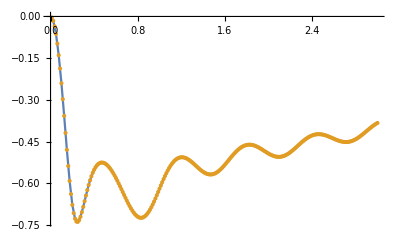

```mathematica
ListPlot[{v2b10,Transpose[{v2kTr01[[All,1]]*0.1,v2kTr01[[All,2,1]]}]},Joined->{True,False}]
```